```mathematica
(* Classical Theory of Heat Capacity      Cv = 3R     *)
```

```mathematica
(* Einstein Theory of Heat Capacity - All Frequencies allowed  *)
```

```mathematica
Cv= 3*8.314
```

24.942

```mathematica
24.942
```

24.942

```mathematica
c= 3.0*10^8; h=6.62*10^-34;k= 1.381*10^-23;T=600;
```

```mathematica
Freq = 500;
```

```mathematica
θE:= h*freq/k;
```

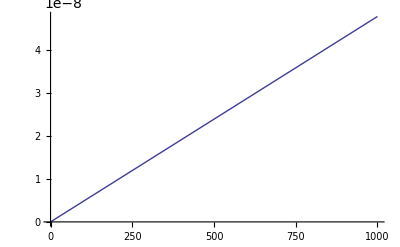

```mathematica
Plot[ h*freq/k,{freq,0,1000}]
```

```mathematica
Plot[θE,{freq,0,1000}]
```

-Graphics-

```mathematica
Na =6.023*10^23
```

6.023×10^23

```mathematica
R=k*Na
```

8.31776

```mathematica
CvEinstein := 3*R*(θE/T)^2 *(Exp[θE/(2*T)]/(Exp[θE/T]-1.0))^2
```

```mathematica
θE= 1.5; T=0.0
```

0.

```mathematica
CvEinstein := 3*R*(θE/T)^2 *(Exp[θE/(2*T)]/(Exp[θE/T]-1.0))^2
```

```mathematica
θE=200
```

200

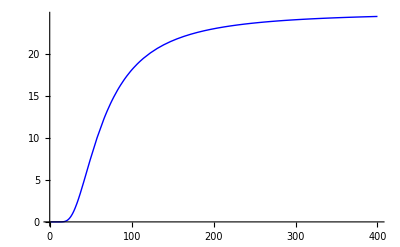

```mathematica
pE= Plot[ CvEinstein,{T,1,400},PlotStyle->Blue]
```

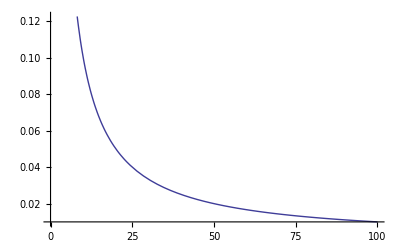

```mathematica
p1=Plot[ 1/x, {x,0,100}]
```

```mathematica
Show[p1]
```

-Graphics-

```mathematica
Show[pE,PlotRange->All]
```

-Graphics-

```mathematica
CvEinsteinxy:= 3*R*(x/yT)^2 *(Exp[x/(2*yT)]/(Exp[x/yT]-1.0))^2
```

```mathematica
Plot3D[CvEinsteinxy,{x,0,400},{yT,0,200}, AxesLabel ->{"θEinsten","Temp"}]
```

-Graphics3D-

```mathematica
Plot3D[ CvEinstein,{T,0,400},{θE,100,400}]
```

-Graphics3D-

```mathematica
Animate[Plot[ 3*R*(θE/T)^2 *(Exp[θE/(2*T)]/(Exp[θE/T]-1.0))^2,{T,0,400}],{θE,100,400},AnimationRunning ->False ]
```

```mathematica
(* Debye Formula  *)
```

```mathematica
θD=100
```

100

```mathematica
R
```

8.31776

```mathematica
e=Exp[1.0]
```

2.71828

```mathematica
T=40
```

40

```mathematica
θDT=θD/T
```

5/2

```mathematica
CvDebye=3*R*3*(θDT)^3* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θDT)}]
```

4543.82

```mathematica
T=10
```

10

```mathematica
θDT=θD/T
```

10

```mathematica
y=θDT
```

10

```mathematica
CvDebye:=3*R*3*(y)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(y)}]
```

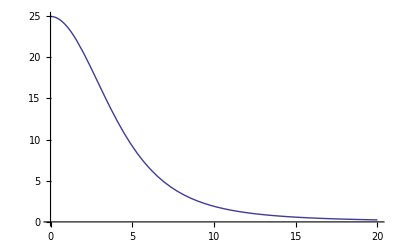

```mathematica
Plot[3*R*3*(θDT)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θDT)}],{θDT,(θD/5),(θD/100000)}]
```

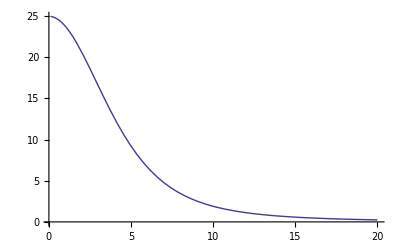

```mathematica
Plot[CvDebye,{y,(θD/5),(θD/1000)}]
```

```mathematica
θD/5
θD/1000
```

20

1/10

```mathematica
Plot[CvDebye,{y,(θD/5),(θD/1000)}]
```

-Graphics-

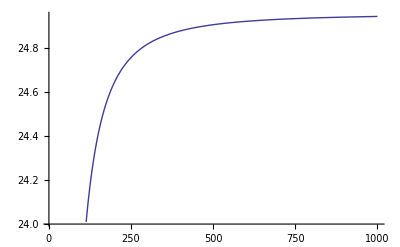

```mathematica
Plot[3*R*3*(θD/q)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θD/q)}],{q,(5),(1000)}]
```

```mathematica
θD=600
```

600

```mathematica
CvDebyeT:=3*R*3*(θD/y)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θD/y)}]
```

```mathematica
θD=600
```

600

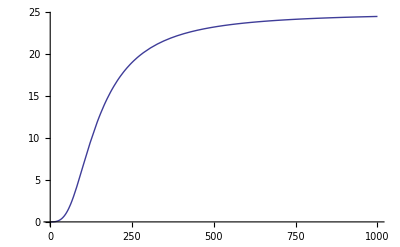

```mathematica
Plot[CvDebyeT,{y,(1),(1000)}]
```

```mathematica
θD=600
```

600

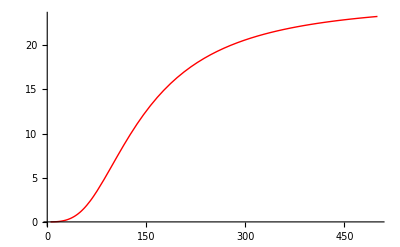

```mathematica
pD= Plot[CvDebyeT,{y,(5),(500)},PlotStyle->Red]
```

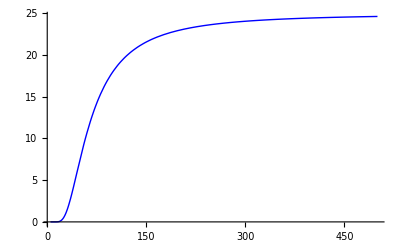

```mathematica
pE= Plot[ CvEinstein,{T,5,500},PlotStyle->Blue]
```

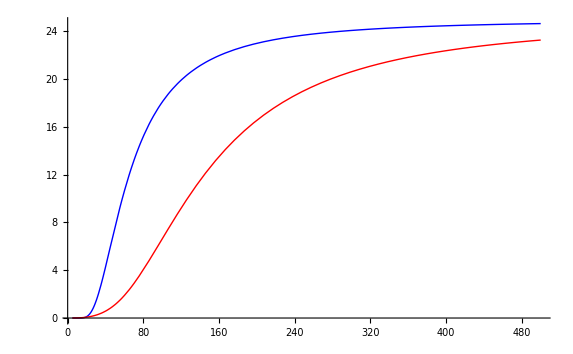

```mathematica
Show[pE,pD,PlotRange->All]
```

```mathematica
CvDebyeT:=3*R*3*(θDx/y)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θDx/y)}];
```

```mathematica
θDx=θD
```

600

```mathematica
Animate[Plot[Exp[y/θDx],{y,(5),(1000)}],{θDx,100,1000},AnimationRunning ->False ]
```

```mathematica
θDx
```

600

```mathematica
Animate[Plot[3*R*3*(θDx/y)^(-3)* NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,(θDx/y)}],{y,(5),(500)}],{θDx,1,400},AnimationRunning ->False ]
```

```mathematica
(* INserting function label didn't work *)
```

```mathematica
Animate[Plot[CvDebyeT,{y,(5),(1000)}],{θDx,1,100},AnimationRunning ->False ]
```

```mathematica
θDx
```

600

```mathematica
NIntegrate  [ x^4*e^x/(e^x-1)^2,{x,0,2}]
```

2.20109

```mathematica
x^4e^x/((e^x-1)^2)
```

(2.71828^x x^4)/((-1+2.71828^x)^2)